## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataN=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/N.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataN//TableForm
```

N | I, A | dA, A | N | N-Nf | d(N-Nf) | 
1. | 0. | 0.02 | 0.66 | -0.13 | 0.12 | 0.
2. | 0.2 | 0.02 | 0.71 | -0.08 | 0.12 | 52.
3. | 0.4 | 0.02 | 0.91 | 0.12 | 0.13 | 103.
4. | 0.6 | 0.02 | 0.89 | 0.1 | 0.13 | 155.
5. | 0.8 | 0.02 | 0.96 | 0.17 | 0.13 | 207.
6. | 1. | 0.02 | 1.37 | 0.58 | 0.14 | 258.
7. | 1.2 | 0.02 | 1.78 | 0.99 | 0.16 | 310.
8. | 1.4 | 0.02 | 2.4 | 1.61 | 0.18 | 362.
9. | 1.7 | 0.02 | 3.52 | 2.73 | 0.21 | 439.
10. | 2. | 0.02 | 3.96 | 3.17 | 0.22 | 517.
11. | 2.3 | 0.02 | 3.97 | 3.18 | 0.22 | 594.
12. | 2.6 | 0.02 | 4.05 | 3.26 | 0.22 | 672.
13. | 2.9 | 0.02 | 3.56 | 2.77 | 0.21 | 749.
14. | 3.2 | 0.02 | 2.57 | 1.78 | 0.18 | 827.
15. | 3.3 | 0.02 | 2.27 | 1.48 | 0.17 | 853.
16. | 3.4 | 0.02 | 1.42 | 0.63 | 0.15 | 878.
17. | 3.6 | 0.02 | 1.3 | 0.51 | 0.14 | 930.
18. | 3.7 | 0.02 | 1. | 0.21 | 0.13 | 956.
19. | 3.8 | 0.02 | 1.14 | 0.35 | 0.14 | 982.
20. | 3.85 | 0.02 | 1.71 | 0.92 | 0.16 | 995.
21. | 3.9 | 0.02 | 2.89 | 2.1 | 0.19 | 1008.
22. | 3.95 | 0.02 | 4.42 | 3.63 | 0.23 | 1020.
23. | 4. | 0.02 | 5.23 | 4.44 | 0.24 | 1033.
24. | 4.1 | 0.02 | 5.11 | 4.32 | 0.24 | 1059.
25. | 4.2 | 0.02 | 4.58 | 3.79 | 0.23 | 1085.
26. | 4.3 | 0.02 | 4.23 | 3.44 | 0.22 | 1111.
27. | 4.33 | 0.02 | 3.38 | 2.59 | 0.2 | 1119.
28. | 4.35 | 0.02 | 2.4 | 1.61 | 0.18 | 1124.
29. | 4.4 | 0.02 | 2.12 | 1.33 | 0.17 | 1137.
30. | 4.5 | 0.02 | 0.9 | 0.11 | 0.13 | 1163.
31. | 4.6 | 0.02 | 0.56 | -0.23 | 0.11 | 1188.
32. | 4.8 | 0.02 | 0.54 | -0.25 | 0.11 | 1240.
33. | 5. | 0.02 | 0.32 | -0.47 | 0.1 | 1292.

### Фитирование табличных данных

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitN=Sort@dataN⟦2;;,{2,5,7}⟧; 
forFitNCr=dataN⟦2;;,6⟧;
model =a*Exp[-(x-b)^2/c^2]+d*x^2*(Max[(f-Sqrt[x^2+e]),0])^2+g;
modelm =a*Exp[-(x-b)^2/c^2]+d*x^2*(f-Sqrt[x^2+e])^2+g;
(*model1 =a*Exp[-(x-e*1.98)^2/c^2]+d*x^2*Max[(f-Sqrt[x^2+e^2])^2,0]+g;*)
(*model1 =a*Exp[-(x-e*1.98)^2/(2 c^2)]+d*x^2*Max[{(f-Sqrt[x^2+e^2])^2+g,0}];*)
```

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fit=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model,1<a<4.5,3<b<4.5,0<c<10, 0.21<d<5, 4<f<10,0<e<10},{{a,5},{b,3.9},{c,0.3},{d,2},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]
(*fitP=NonlinearModelFit[forFitN⟦All,{3,2}⟧,{modelm(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{{a,4.5},{b,1000},{c,100},{d,3},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]*)
fit@"ParameterTable"
(*fitP@"ParameterTable"*)
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
degOfFree=7;
χ=√(Total[(fit["FitResiduals"]/forFitNCr)^2]/(Length[forFitN]-degOfFree));
χ^2
```

FittedModel[-0.292866+4.5 ⅇ^(-13.8257 (-«18»+x)^2)+0.391709 x^2 Max[0,5.18744-√(9.9997+x^2)]^2]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.5 | 0.339283 | 13.2633 | 4.42017×10^-13
b | 4.1249 | 0.0155061 | 266.018 | 3.4296×10^-46
c | 0.26894 | 0.0234392 | 11.4739 | 1.12456×10^-11
d | 0.391709 | 0.632318 | 0.619481 | 0.540991
f | 5.18744 | 2.46404 | 2.10526 | 0.0450824
e | 9.9997 | 27.2254 | 0.367292 | 0.716374
g | -0.292866 | 0.187225 | -1.56425 | 0.12985

7.00407

```mathematica
fit["BestFitParameters"]
```

{a→4.80213,b→4.11697,c→0.171005,d→1.10696,f→13.2912,e→145.844,g→-0.471867}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicXN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicYN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

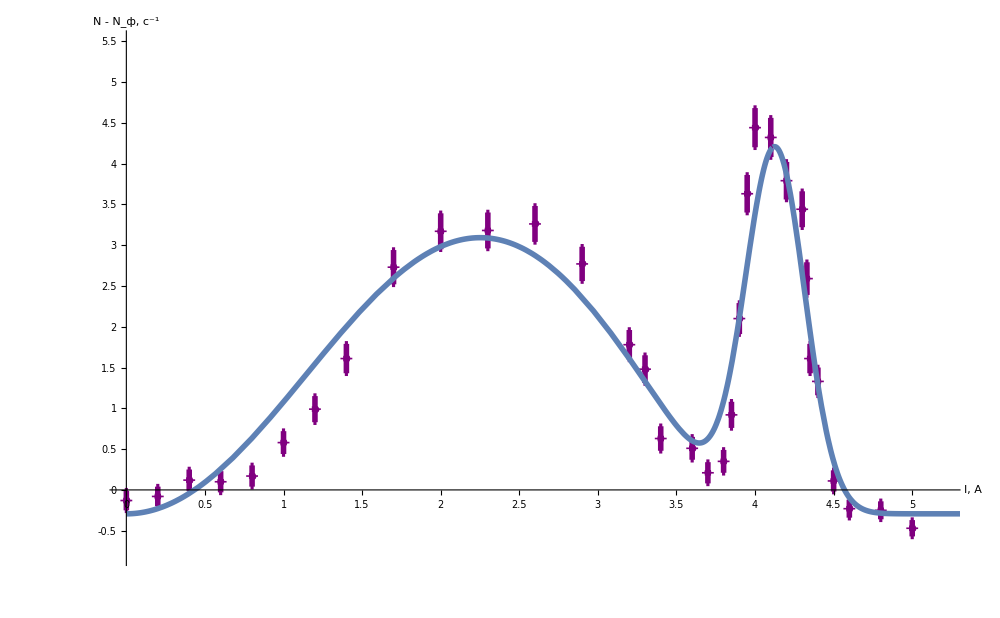

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{2,5,3,6}⟧,
GridLines->{grids@0.25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"I, A","N - N_(:0444), (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicXN,myTicYN},
PlotRange->{{0,5.2},{-0.8,5.5}}], 
Plot[fit["Function"]@x,{x,0,5.6}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

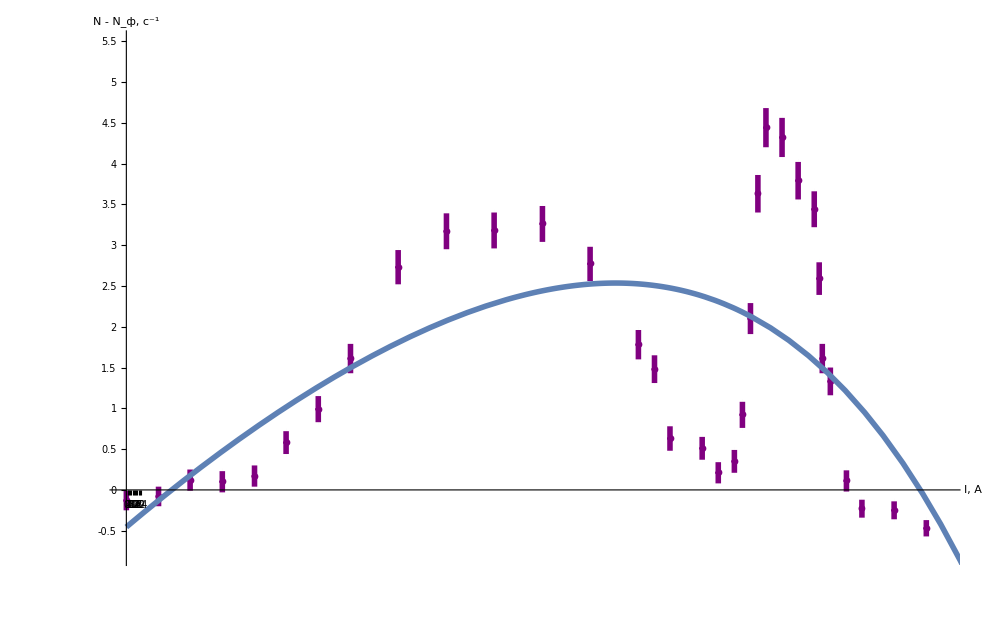

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{7,5,3,6}⟧,
GridLines->{grids@25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"I, A","N - N_(:0444), (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicXN,myTicYN},
PlotRange->{{0,1320},{-0.8,5.5}}], 
Plot[fitP["Function"]@x,{x,0,1500}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

### Импорт табличных данных

```mathematica
dataK=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/kir.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataK//TableForm
```

I | sigI | N | sigN | p | T
0.02 | 0.02 | 1.469 | 0.121202 | 5.74157 | 0.032255
0.2 | 0.02 | 1.639 | 0.128023 | 57.4157 | 3.21549
0.4 | 0.02 | 1.539 | 0.124056 | 114.831 | 12.7435
0.6 | 0.02 | 1.679 | 0.129576 | 172.247 | 28.2496
0.8 | 0.02 | 1.929 | 0.138888 | 229.663 | 49.2375
1. | 0.02 | 2.139 | 0.146253 | 287.079 | 75.1187
1.1 | 0.02 | 2.769 | 0.166403 | 315.787 | 89.7014
1.2 | 0.02 | 2.909 | 0.170558 | 344.494 | 105.277
1.4 | 0.02 | 3.159 | 0.177736 | 401.91 | 139.117
1.6 | 0.02 | 3.489 | 0.186789 | 459.326 | 176.096
1.8 | 0.02 | 3.619 | 0.190237 | 516.742 | 215.734
2. | 0.02 | 3.809 | 0.195167 | 574.157 | 257.621
2.2 | 0.02 | 3.929 | 0.198217 | 631.573 | 301.407
2.4 | 0.02 | 3.539 | 0.188122 | 688.989 | 346.803
2.6 | 0.02 | 3.059 | 0.1749 | 746.404 | 393.567
2.8 | 0.02 | 2.779 | 0.166703 | 803.82 | 441.496
3. | 0.02 | 2.519 | 0.158714 | 861.236 | 490.423
3.1 | 0.02 | 2.759 | 0.166102 | 889.944 | 515.217
3.2 | 0.02 | 2.679 | 0.163677 | 918.652 | 540.21
3.25 | 0.02 | 3.059 | 0.1749 | 933.006 | 552.777
3.3 | 0.02 | 3.619 | 0.190237 | 947.36 | 565.388
3.35 | 0.02 | 3.639 | 0.190762 | 961.713 | 578.043
3.4 | 0.02 | 4.079 | 0.201965 | 976.067 | 590.739
3.45 | 0.02 | 4.049 | 0.201221 | 990.421 | 603.475
3.5 | 0.02 | 4.618 | 0.214895 | 1004.78 | 616.251
3.55 | 0.02 | 4.208 | 0.205134 | 1019.13 | 629.064
3.6 | 0.02 | 3.859 | 0.196443 | 1033.48 | 641.913
3.65 | 0.02 | 3.899 | 0.197459 | 1047.84 | 654.797
3.7 | 0.02 | 4.248 | 0.206107 | 1062.19 | 667.716
3.75 | 0.02 | 3.649 | 0.191024 | 1076.54 | 680.667
3.8 | 0.02 | 3.139 | 0.177172 | 1090.9 | 693.65
3.9 | 0.02 | 2.369 | 0.153916 | 1119.61 | 719.707
4. | 0.02 | 1.389 | 0.117856 | 1148.31 | 745.88
4.1 | 0.02 | 1.23 | 0.110905 | 1177.02 | 772.161
4.2 | 0.02 | 0.84 | 0.0916515 | 1205.73 | 798.544
4.3 | 0.02 | 0.818 | 0.0904434 | 1234.44 | 825.023
4.4 | 0.02 | 0.74 | 0.0860233 | 1263.15 | 851.593

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXkir=MapAt[dropLastDot@*ToString,dataK,{{2;;,All}}];
forTeXkir//TeXForm
```

\left(
\begin{array}{cccccc}
 \text{I} & \text{sigI} & \text{N} & \text{sigN} & \text{p} & \text{T} \\
 0.02 & 0.02 & 1.469 & 0.121202 & 5.74157 & 0.032255 \\
 0.2 & 0.02 & 1.639 & 0.128023 & 57.4157 & 3.21549 \\
 0.4 & 0.02 & 1.539 & 0.124056 & 114.831 & 12.7435 \\
 0.6 & 0.02 & 1.679 & 0.129576 & 172.247 & 28.2496 \\
 0.8 & 0.02 & 1.929 & 0.138888 & 229.663 & 49.2375 \\
 1 & 0.02 & 2.139 & 0.146253 & 287.079 & 75.1187 \\
 1.1 & 0.02 & 2.769 & 0.166403 & 315.787 & 89.7014 \\
 1.2 & 0.02 & 2.909 & 0.170558 & 344.494 & 105.277 \\
 1.4 & 0.02 & 3.159 & 0.177736 & 401.91 & 139.117 \\
 1.6 & 0.02 & 3.489 & 0.186789 & 459.326 & 176.096 \\
 1.8 & 0.02 & 3.619 & 0.190237 & 516.742 & 215.734 \\
 2 & 0.02 & 3.809 & 0.195167 & 574.157 & 257.621 \\
 2.2 & 0.02 & 3.929 & 0.198217 & 631.573 & 301.407 \\
 2.4 & 0.02 & 3.539 & 0.188122 & 688.989 & 346.803 \\
 2.6 & 0.02 & 3.059 & 0.1749 & 746.404 & 393.567 \\
 2.8 & 0.02 & 2.779 & 0.166703 & 803.82 & 441.496 \\
 3 & 0.02 & 2.519 & 0.158714 & 861.236 & 490.423 \\
 3.1 & 0.02 & 2.759 & 0.166102 & 889.944 & 515.217 \\
 3.2 & 0.02 & 2.679 & 0.163677 & 918.652 & 540.21 \\
 3.25 & 0.02 & 3.059 & 0.1749 & 933.006 & 552.777 \\
 3.3 & 0.02 & 3.619 & 0.190237 & 947.36 & 565.388 \\
 3.35 & 0.02 & 3.639 & 0.190762 & 961.713 & 578.043 \\
 3.4 & 0.02 & 4.079 & 0.201965 & 976.067 & 590.739 \\
 3.45 & 0.02 & 4.049 & 0.201221 & 990.421 & 603.475 \\
 3.5 & 0.02 & 4.618 & 0.214895 & 1004.78 & 616.251 \\
 3.55 & 0.02 & 4.208 & 0.205134 & 1019.13 & 629.064 \\
 3.6 & 0.02 & 3.859 & 0.196443 & 1033.48 & 641.913 \\
 3.65 & 0.02 & 3.899 & 0.197459 & 1047.84 & 654.797 \\
 3.7 & 0.02 & 4.248 & 0.206107 & 1062.19 & 667.716 \\
 3.75 & 0.02 & 3.649 & 0.191024 & 1076.54 & 680.667 \\
 3.8 & 0.02 & 3.139 & 0.177172 & 1090.9 & 693.65 \\
 3.9 & 0.02 & 2.369 & 0.153916 & 1119.61 & 719.707 \\
 4 & 0.02 & 1.389 & 0.117856 & 1148.31 & 745.88 \\
 4.1 & 0.02 & 1.23 & 0.110905 & 1177.02 & 772.161 \\
 4.2 & 0.02 & 0.84 & 0.0916515 & 1205.73 & 798.544 \\
 4.3 & 0.02 & 0.818 & 0.0904434 & 1234.44 & 825.023 \\
 4.4 & 0.02 & 0.74 & 0.0860233 & 1263.15 & 851.593 \\
\end{array}
\right)